Run the below cell to load the library and make sure the Graph outputs are formatted nicely

#### Importing library

```mathematica
Import[NotebookDirectory[]<>"library_graphStates.m"]
```

```mathematica
style={VertexShapeFunction->"Circle",VertexStyle->Directive[EdgeForm[{Thick,Black}],LightPurple],EdgeStyle->Directive[Black,Thick],VertexLabels->Placed["Name",{1/2,1/2}],VertexLabelStyle->Directive[Black,FontFamily->"Times",15],VertexSize->0.4};
```

# Graph exploring

#### Initial graphs

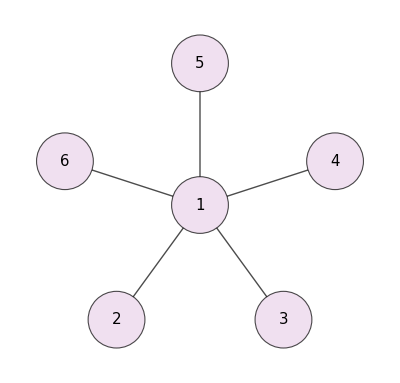
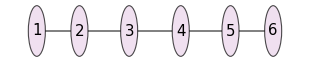
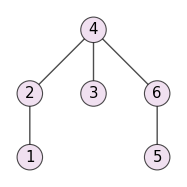
```mathematica
-Graphics--Graphics--Graphics--Graphics-
```

#### Some useful functions for exploring graphs

```mathematica
?FindLUequivalent
```

```mathematica
?Zmeasurement
```

```mathematica
?Xmeasurement
```

```mathematica
?Ymeasurement
```

```mathematica
?LUfamily
```

### Ring graph (LC equivalent to Butterfly)

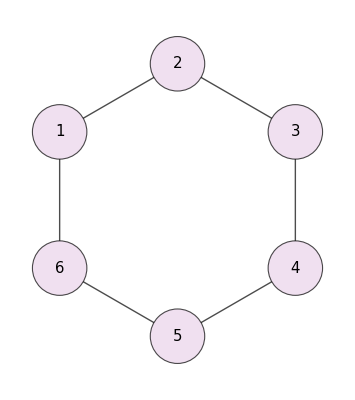
```mathematica
LUfamily[-Graphics-]
```

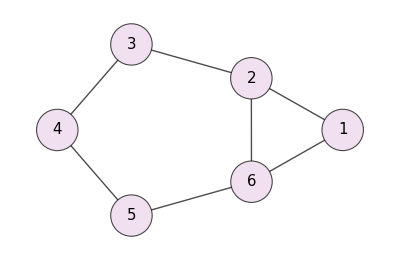
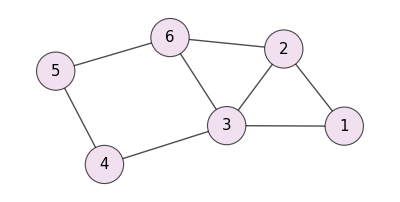
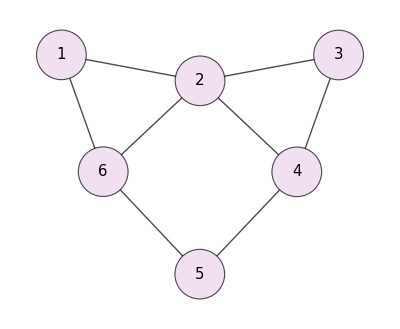
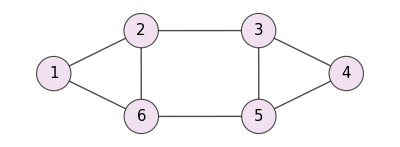
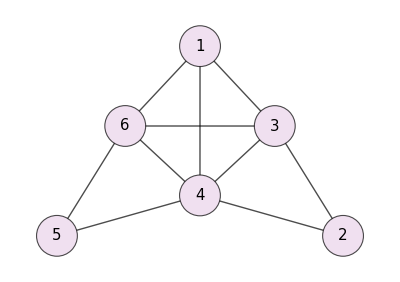
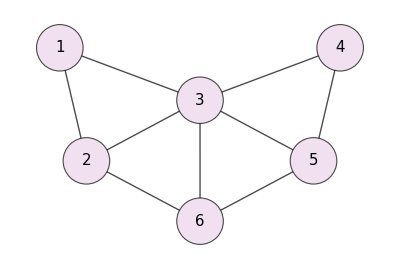
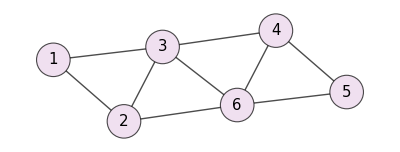
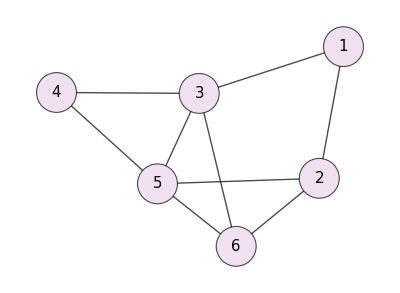
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

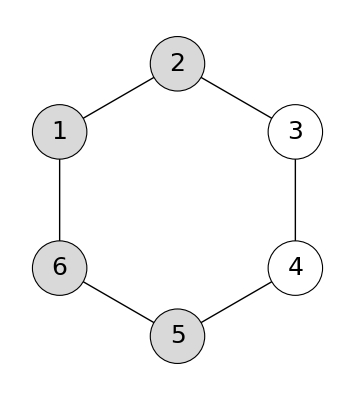
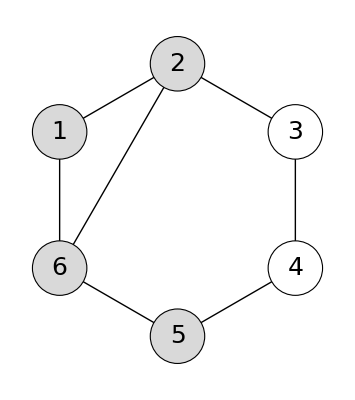
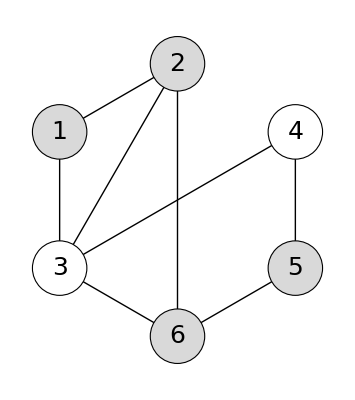
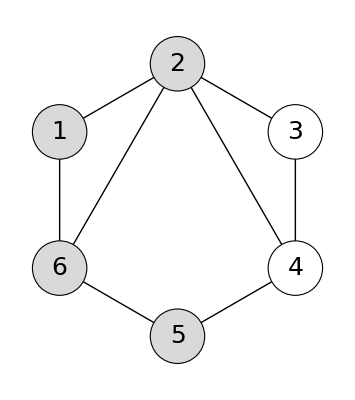
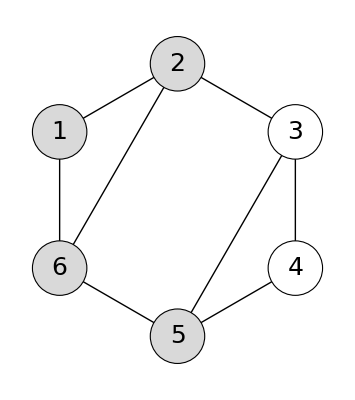
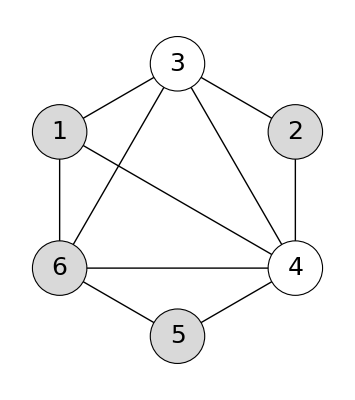
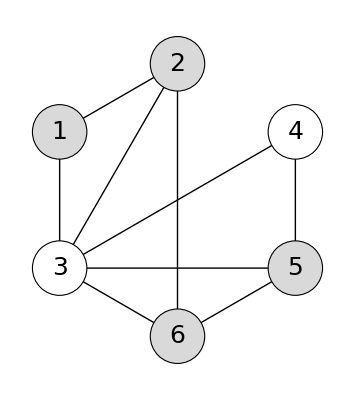
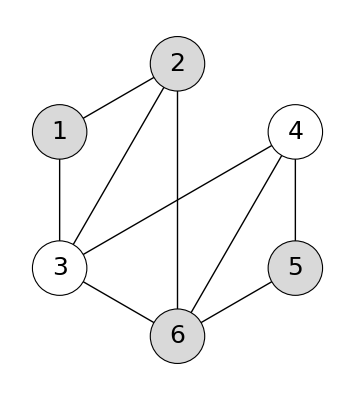

```mathematica
CustomGraphStyle/@{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

### Star graph

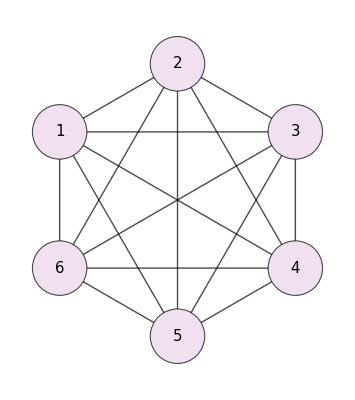
{-Graphics-,-Graphics-}

```mathematica
LUfamily[-Graphics-]
```

```mathematica
CustomGraphStyle/@{-Graphics-,-Graphics-}
```

### Linear cluster

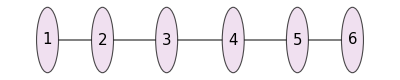
```mathematica
LUfamily[-Graphics-]
```

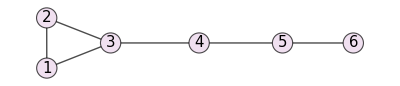
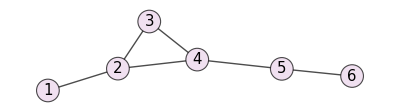
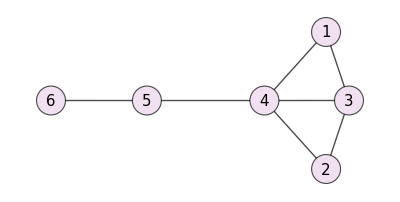
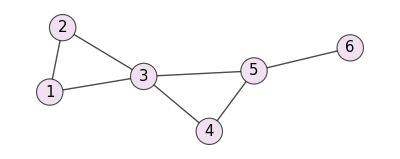
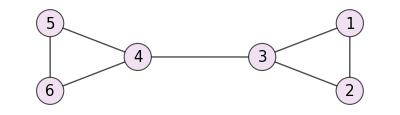
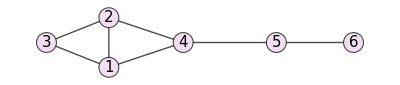
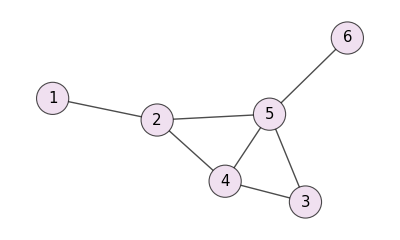
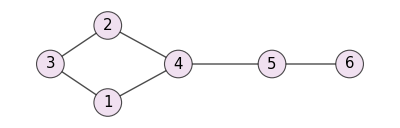
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

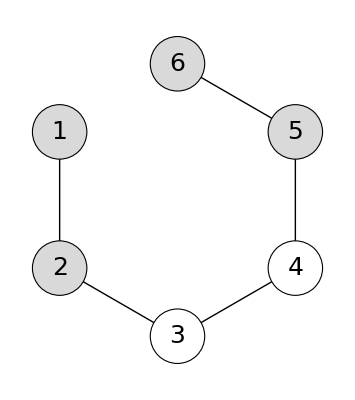
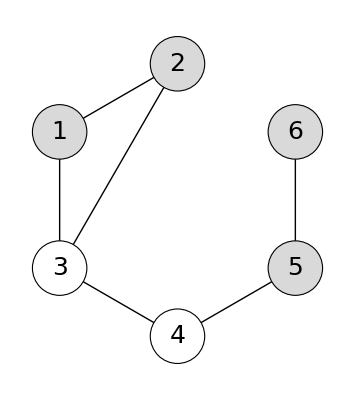
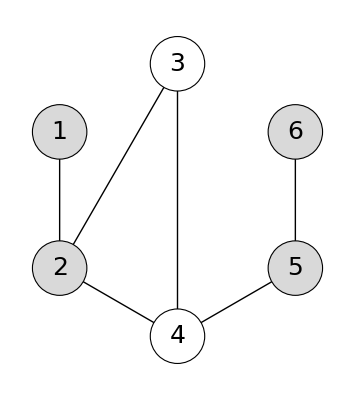
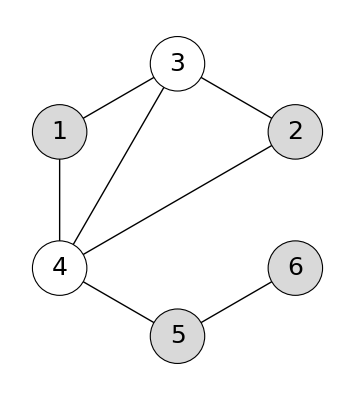
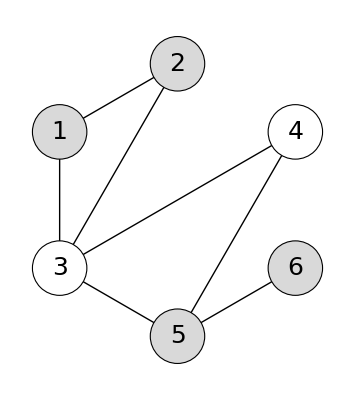
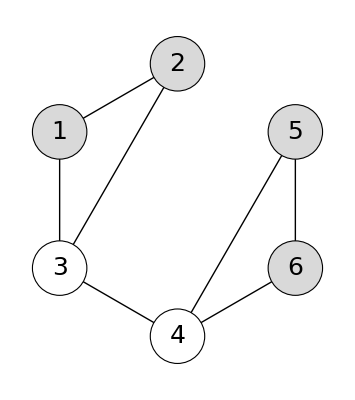
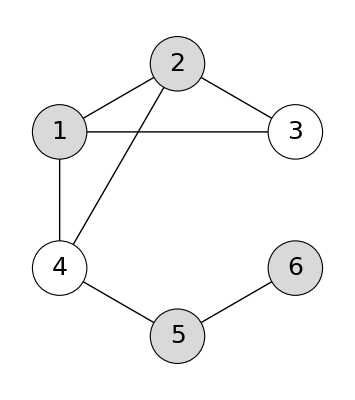
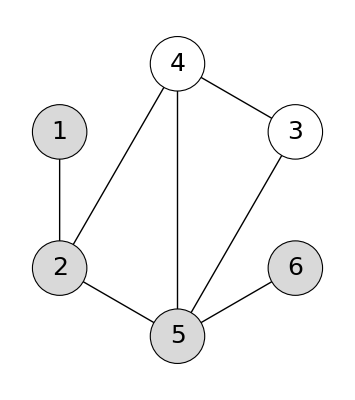
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
CustomGraphStyle/@{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

### Trident

```mathematica
LUfamily[-Graphics-]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
CustomGraphStyle/@{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Example

Ring graph is LC equivalent to the butterfly. The following is the example mash used in his thesis.

### Ring graph to Butterfly and then to Bell and GHZ

```mathematica
FindLUequivalent[-Graphics-,1]
```

-Graphics-

```mathematica
FindLUequivalent[-Graphics-,2]
```

-Graphics-

```mathematica
FindLUequivalent[-Graphics-,1]
```

-Graphics-

#### Using the ring graph: Performing Z measurement on 2 to get to linear cluster and 5 to get to Bell pairs

```mathematica
{Zmeasurement[-Graphics-,2],Zmeasurement[-Graphics-,5]}
```

{-Graphics-,-Graphics-}

#### Using the butterfly graph: Performing Z measurement on 2 and 5 to get to GHZ

```mathematica
{Zmeasurement[-Graphics-,2],Zmeasurement[-Graphics-,5]}
```

{-Graphics-,-Graphics-}